# Bass model

## The model

Provided constants p and q,

```mathematica
F'[t]==(p+q F[t])(1-F[t]);
```

where 0 ≤ F[t] ≤ 1.

## Interpretation

F’[t] is the rate of adoption in a certain population yielding F[t] as an S-shaped curve. Here, constants p represent the rate of spontaneous innovation/adoption and q the rate of imitation of adoption. The portion 1-F[t] decreases faster when F’[t] is large.

## Solution

A solution for this differential equation is

```mathematica
F[t_,p_,q_]:=(1-Exp[-(p+q)t])/(1+p /q*Exp[-(p+q)t]);
```

## Example 1

```mathematica
Manipulate[Plot[F[t,p,q],{t,0,10},PlotRange->Full],{{p,1/3},0,1},{{q,2/3},p,1}]
```

## Example 2

```mathematica
k=DSolve[{f'[t]==p+(q-p) f[t]-q f[t]^2,f[0]==0},f,t];
g[x_?NumericQ]:=(f/.k[[1]]/.{p->1/3,q->2/3})[x];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

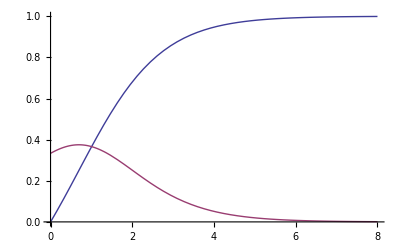

```mathematica
Plot[{g[t],g'[t]},{t,0,8},PlotRange->Full]
```

## Comments

In a network, diffusion forms a graph containing a giant component, whose size varies between

```mathematica
1/n<p<Log[n]/n
```

where
p << 1/n: all nodes isoleted (little diffusion)
log(n)/n << p: all paths are connected.